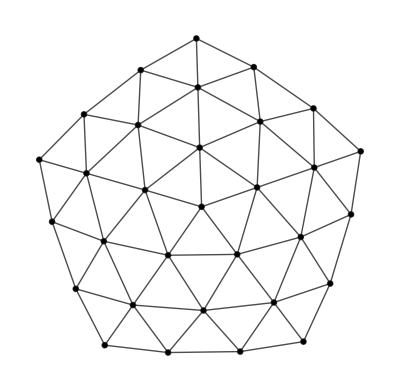

```mathematica
(*C_{6} -60*)Graph[{0<->1,0<->2,0<->3,0<->4,0<->5,1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,2<->7,3<->7,3<->8,4<->8,4<->9,5<->9,5<->10,1<->10,1<->11,2<->12,3<->13,4<->14,5<->15,6<->11,6<->12,7<->12,7<->13,8<->13,8<->14,9<->14,9<->15,10<->11,10<->15,6<->16,6<->17,7<->18,7<->19,8<->20,8<->21,9<->22,9<->23,10<->24,10<->25,16<->17,11<->16,11<->25,12<->17,12<->18,18<->19,13<->19,13<->21,21<->20,14<->20,14<->23,24<->25,22<->23,15<->22,24<->15,11<->26,12<->27,13<->28,14<->29,15<->30,25<->26,16<->26,17<->27,18<->27,19<->28,21<->28,20<->29,23<->29,24<->30,22<->30},EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

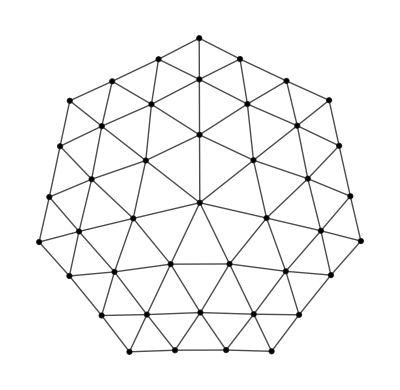

```mathematica
(*C_{6} +60*)Graph[{0<->1,0<->2,0<->3,0<->4,0<->5,0<->6,0<->7,1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->1,1<->8,1<->9,1<->10,8<->9,9<->10,2<->10,7<->8,2<->11,2<->12,10<->11,11<->12,3<->12,3<->13,3<->14,12<->13,13<->14,4<->14,4<->15,4<->16,14<->15,15<->16,5<->16,5<->17,5<->18,16<->17,17<->18,6<->18,6<->19,6<->20,18<->19,19<->20,7<->20,7<->21,20<->21,21<->8,22<->8,22<->21,22<->23,23<->8,23<->9,23<->24,24<->9,24<->25,25<->9,25<->10,25<->26,26<->10,26<->11,26<->27,27<->11,27<->28,28<->11,28<->12,28<->29,29<->12,29<->13,29<->30,30<->13,30<->31,31<->13,31<->14,31<->32,32<->14,32<->15,32<->33,33<->15,33<->34,34<->15,34<->16,34<->35,35<->16,35<->17,35<->36,36<->17,36<->37,37<->17,37<->18,37<->38,38<->18,38<->19,38<->39,39<->19,39<->40,40<->19,40<->20,40<->41,41<->20,41<->21,41<->42,42<->21,42<->22},EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

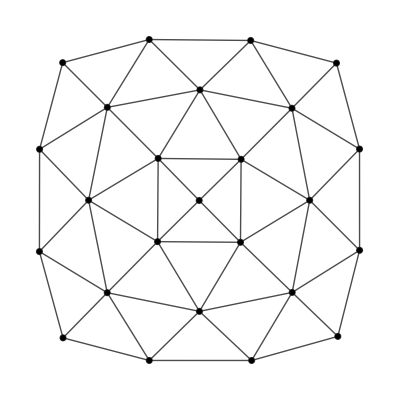

```mathematica
(*C_{3} +-120 [a]=0*)
disc={0<->{1,1},0<->{1,2},0<->{1,3},0<->{1,4}};
For[i=1,i≤4,i++,For[k=1,k<4i,k++,AppendTo[disc,{i,k}<->{i,k+1}]];
AppendTo[disc,{i,1}<->{i,4i}];
AppendTo[disc,{i,1}<->{i+1,1}];
AppendTo[disc,{i,1}<->{i+1,2}];
AppendTo[disc,{i,1}<->{i+1,4i+4}];
AppendTo[disc,{i,i+1}<->{i+1,i+1}];
AppendTo[disc,{i,i+1}<->{i+1,i+2}];
AppendTo[disc,{i,i+1}<->{i+1,i+3}];
AppendTo[disc,{i,2i+1}<->{i+1,2i+2}];
AppendTo[disc,{i,2i+1}<->{i+1,2i+3}];
AppendTo[disc,{i,2i+1}<->{i+1,2i+4}];
AppendTo[disc,{i,3i+1}<->{i+1,3i+3}];
AppendTo[disc,{i,3i+1}<->{i+1,3i+4}];
AppendTo[disc,{i,3i+1}<->{i+1,3i+5}];
If[i≥2,For[j=2,j≤i,j++,AppendTo[disc,{i,j}<->{i+1,j}];AppendTo[disc,{i,j}<->{i+1,j+1}]];For[j=i+2,j≤2i,j++,AppendTo[disc,{i,j}<->{i+1,j+1}];AppendTo[disc,{i,j}<->{i+1,j+2}]];For[j=2i+2,j≤3i,j++,AppendTo[disc,{i,j}<->{i+1,j+2}];AppendTo[disc,{i,j}<->{i+1,j+3}]];For[j=3i+2,j≤4i,j++,AppendTo[disc,{i,j}<->{i+1,j+3}];AppendTo[disc,{i,j}<->{i+1,j+4}]]]]
L=3;
disc=disc[[1;;Sum[4i,{i,1,L}]+Sum[8i+4,{i,0,L-1}]]];
Graph[disc,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

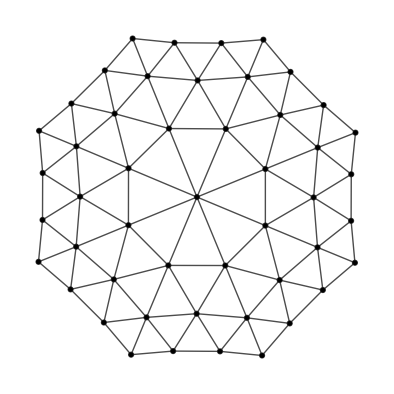

```mathematica
disc={0<->{1,1},0<->{1,2},0<->{1,3},0<->{1,4},0<->{1,5},0<->{1,6},0<->{1,7},0<->{1,8}};
For[i=1,i≤4,i++,For[k=1,k<8i,k++,AppendTo[disc,{i,k}<->{i,k+1}]];
AppendTo[disc,{i,1}<->{i,8i}];
AppendTo[disc,{i,1}<->{i+1,1}];
AppendTo[disc,{i,1}<->{i+1,2}];
AppendTo[disc,{i,1}<->{i+1,8i+8}];
AppendTo[disc,{i,i+1}<->{i+1,i+1}];
AppendTo[disc,{i,i+1}<->{i+1,i+2}];
AppendTo[disc,{i,i+1}<->{i+1,i+3}];
AppendTo[disc,{i,2i+1}<->{i+1,2i+2}];
AppendTo[disc,{i,2i+1}<->{i+1,2i+3}];
AppendTo[disc,{i,2i+1}<->{i+1,2i+4}];
AppendTo[disc,{i,3i+1}<->{i+1,3i+3}];
AppendTo[disc,{i,3i+1}<->{i+1,3i+4}];
AppendTo[disc,{i,3i+1}<->{i+1,3i+5}];
AppendTo[disc,{i,4i+1}<->{i+1,4i+4}];
AppendTo[disc,{i,4i+1}<->{i+1,4i+5}];
AppendTo[disc,{i,4i+1}<->{i+1,4i+6}];
AppendTo[disc,{i,5i+1}<->{i+1,5i+5}];
AppendTo[disc,{i,5i+1}<->{i+1,5i+6}];
AppendTo[disc,{i,5i+1}<->{i+1,5i+7}];
AppendTo[disc,{i,6i+1}<->{i+1,6i+6}];
AppendTo[disc,{i,6i+1}<->{i+1,6i+7}];
AppendTo[disc,{i,6i+1}<->{i+1,6i+8}];
AppendTo[disc,{i,7i+1}<->{i+1,7i+7}];
AppendTo[disc,{i,7i+1}<->{i+1,7i+8}];
AppendTo[disc,{i,7i+1}<->{i+1,7i+9}];
If[i≥2,For[j=2,j≤i,j++,AppendTo[disc,{i,j}<->{i+1,j}];AppendTo[disc,{i,j}<->{i+1,j+1}]];For[j=i+2,j≤2i,j++,AppendTo[disc,{i,j}<->{i+1,j+1}];AppendTo[disc,{i,j}<->{i+1,j+2}]];For[j=2i+2,j≤3i,j++,AppendTo[disc,{i,j}<->{i+1,j+2}];AppendTo[disc,{i,j}<->{i+1,j+3}]];For[j=3i+2,j≤4i,j++,AppendTo[disc,{i,j}<->{i+1,j+3}];AppendTo[disc,{i,j}<->{i+1,j+4}]];
For[j=4i+2,j≤5i,j++,AppendTo[disc,{i,j}<->{i+1,j+4}];AppendTo[disc,{i,j}<->{i+1,j+5}]];For[j=5i+2,j≤6i,j++,AppendTo[disc,{i,j}<->{i+1,j+5}];AppendTo[disc,{i,j}<->{i+1,j+6}]];For[j=6i+2,j≤7i,j++,AppendTo[disc,{i,j}<->{i+1,j+6}];AppendTo[disc,{i,j}<->{i+1,j+7}]];For[j=7i+2,j≤8i,j++,AppendTo[disc,{i,j}<->{i+1,j+7}];AppendTo[disc,{i,j}<->{i+1,j+8}]]]]
L=3;
disc=disc[[1;;Sum[8i,{i,1,L}]+Sum[16i+8,{i,0,L-1}]]];
Graph[disc,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

```mathematica
(*C_{3} +-120 [a]=+-1*)
```

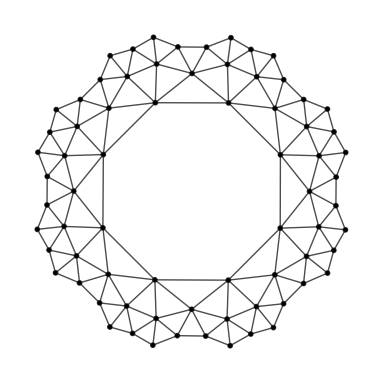

```mathematica
disc={};
For[i=1,i≤2,i++,For[k=1,k<8(2i-1),k++,AppendTo[disc,{i,k}<->{i,k+1}]];AppendTo[disc,{i,1}<->{i,8(2i-1)}];
AppendTo[disc,{i,1}<->{i+1,1}];
AppendTo[disc,{i,1}<->{i+1,2}];
AppendTo[disc,{i,1}<->{i+1,8(2i+1)-1}];
AppendTo[disc,{i,1}<->{i+1,8(2i+1)}];
For[j=2,j≤8(2i-1),j++,AppendTo[disc,{i,j}<->{i+1,j+2(j-2)}];AppendTo[disc,{i,j}<->{i+1,j+2(j-2)+1}];AppendTo[disc,{i,j}<->{i+1,j+2(j-2)+2}];AppendTo[disc,{i,j}<->{i+1,j+2(j-2)+3}]]]
disc=disc[[1;;64]];
For[i=2,i≤23,i=i+3,AppendTo[disc,{2,i}<->{3,i}];AppendTo[disc,{2,i}<->{3,i+1}];AppendTo[disc,{3,i}<->{2,i-1}];AppendTo[disc,{3,i+1}<->{2,i+1}];AppendTo[disc,{3,i}<->{3,i+1}]]
AppendTo[disc,{2,1}<->{3,1}];AppendTo[disc,{2,1}<->{3,40}];AppendTo[disc,{3,1}<->{3,2}];AppendTo[disc,{3,1}<->{3,40}];AppendTo[disc,{3,40}<->{2,24}];
AppendTo[disc,{2,3}<->{3,4}];AppendTo[disc,{3,3}<->{3,4}];AppendTo[disc,{2,4}<->{3,4.5}];AppendTo[disc,{2,3}<->{3,4.5}];AppendTo[disc,{3,4}<->{3,4.5}];
AppendTo[disc,{2,4}<->{3,4.6}];AppendTo[disc,{3,4.6}<->{3,4.5}];AppendTo[disc,{3,4.6}<->{3,5}];AppendTo[disc,{2,6}<->{3,7}];AppendTo[disc,{3,6}<->{3,7}];
AppendTo[disc,{3,7}<->{3,7.5}];AppendTo[disc,{2,6}<->{3,7.5}];AppendTo[disc,{2,7}<->{3,7.5}];AppendTo[disc,{3,7.5}<->{3,7.6}];
AppendTo[disc,{2,7}<->{3,7.6}];AppendTo[disc,{3,7.6}<->{3,8}];AppendTo[disc,{2,9}<->{3,10}];AppendTo[disc,{3,9}<->{3,10}];AppendTo[disc,{2,9}<->{3,10.5}];
AppendTo[disc,{3,10}<->{3,10.5}];AppendTo[disc,{2,10}<->{3,10.5}];AppendTo[disc,{3,10.6}<->{3,10.5}];AppendTo[disc,{2,10}<->{3,10.6}];
AppendTo[disc,{3,10.6}<->{3,11}];AppendTo[disc,{2,12}<->{3,13}];AppendTo[disc,{3,12}<->{3,13}];AppendTo[disc,{2,12}<->{3,13.5}];
AppendTo[disc,{3,13}<->{3,13.5}];AppendTo[disc,{2,13}<->{3,13.5}];AppendTo[disc,{2,13}<->{3,13.6}];AppendTo[disc,{3,13.6}<->{3,13.5}];
AppendTo[disc,{3,13.6}<->{3,14}];AppendTo[disc,{2,15}<->{3,16}];AppendTo[disc,{3,15}<->{3,15.5}];AppendTo[disc,{3,15.5}<->{3,16}];
AppendTo[disc,{3,16}<->{3,16.5}];AppendTo[disc,{2,15}<->{3,15.5}];
AppendTo[disc,{2,16}<->{3,16.5}];AppendTo[disc,{3,17}<->{3,16.5}];AppendTo[disc,{3,16}<->{2,16}];
AppendTo[disc,{2,18}<->{3,19}];AppendTo[disc,{3,18}<->{3,19}];AppendTo[disc,{3,19.5}<->{3,19}];
AppendTo[disc,{3,19.5}<->{2,18}];AppendTo[disc,{3,19.5}<->{2,19}];AppendTo[disc,{3,19.6}<->{3,19.5}];
AppendTo[disc,{3,19.6}<->{2,19}];AppendTo[disc,{3,19.6}<->{3,20}];AppendTo[disc,{3,22}<->{2,21}];AppendTo[disc,{3,22}<->{3,21}];
AppendTo[disc,{3,22}<->{3,22.5}];AppendTo[disc,{3,22.5}<->{2,21}];AppendTo[disc,{3,22.5}<->{2,22}];AppendTo[disc,{3,22.6}<->{2,22}];
AppendTo[disc,{3,22.6}<->{3,22.5}];AppendTo[disc,{3,22.6}<->{3,23}];AppendTo[disc,{3,25}<->{2,24}];AppendTo[disc,{3,25}<->{3,24}];
AppendTo[disc,{3,25}<->{3,40}];
Graph[disc,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black,VertexSize->0.2]
```

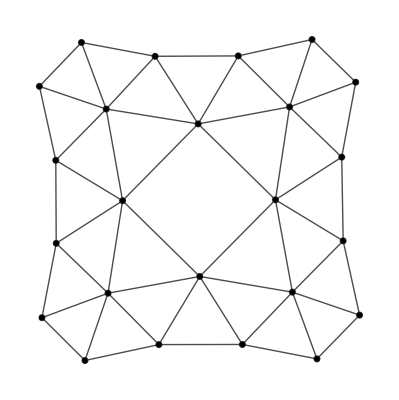

```mathematica
disc={};
For[i=1,i≤1,i++,For[k=1,k<4(2i-1),k++,AppendTo[disc,{i,k}<->{i,k+1}]];AppendTo[disc,{i,1}<->{i,4(2i-1)}];
AppendTo[disc,{i,1}<->{i+1,1}];
AppendTo[disc,{i,1}<->{i+1,2}];
AppendTo[disc,{i,1}<->{i+1,4(2i+1)-1}];
AppendTo[disc,{i,1}<->{i+1,4(2i+1)}];]
For[j=2,j≤4,j++,AppendTo[disc,{1,j}<->{2,j+2(j-2)}];AppendTo[disc,{1,j}<->{2,j+2(j-2)+1}];AppendTo[disc,{1,j}<->{2,j+2(j-2)+2}];AppendTo[disc,{1,j}<->{2,j+2(j-2)+3}]]
For[i=1,i<12,i++,AppendTo[disc,{2,i}<->{2,i+1}]]
AppendTo[disc,{2,1}<->{2,12}];
For[i=2,i≤11,i=i+3,AppendTo[disc,{2,i}<->{3,i}];AppendTo[disc,{2,i}<->{3,i+1}];AppendTo[disc,{3,i}<->{3,i+1}];;AppendTo[disc,{3,i}<->{2,i-1}];AppendTo[disc,{3,i+1}<->{2,i+1}]]
Graph[disc,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

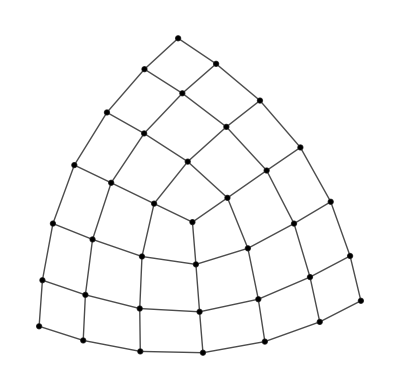

```mathematica
(*C_{4} +-90 [a]=0*)
disc1={0<->{1,2},0<->{1,4},0<->{1,6}};
For[i=1,i≤4,i++,For[k=1,k≤6i-1,k++,AppendTo[disc1,{i,k}<->{i,k+1}]];AppendTo[disc1,{i,6i}<->{i,1}];For[j=1,j≤2i+1,j++,AppendTo[disc1,{i,j}<->{i+1,j+1}]];For[j=2i+1,j≤4i+1,j++,AppendTo[disc1,{i,j}<->{i+1,j+3}]];For[j=4i+1,j≤6i,j++,AppendTo[disc1,{i,j}<->{i+1,j+5}]];
AppendTo[disc1,{i,1}<->{i+1,6(i+1)}]]
L=3;
disc1=disc1[[1;;3L(L+1)+Sum[3(2i-1),{i,1,L}]]];
Graph[disc1,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

```mathematica
AbsoluteOptions[%,VertexCoordinates]
```

{VertexCoordinates→{{2.94466,2.51258},{2.20807,2.86841},{3.61679,2.9798},{3.01103,1.69946},{1.97553,1.85125},{2.85412,3.67664},{4.00932,2.00868},{1.02615,2.1798},{1.3839,3.26913},{2.01666,4.21902},{3.59617,4.34543},{4.36957,3.50545},{4.89532,2.48444},{4.20963,1.02945},{3.0815,0.787285},{1.93248,0.849924},{0.888685,1.11322},{2.75065,4.99114},{5.20223,1.45562},{0.0635588,1.39491},{0.265231,2.48485},{0.676183,3.60975},{1.30279,4.62269},{2.02321,5.45512},{3.39906,5.55807},{4.24121,4.85139},{5.01788,3.94932},{5.60009,2.90398},{5.97196,1.86124},{5.38944,0.593099},{4.33525,0.213859},{3.14638,0.},{1.94303,0.0251824},{0.846909,0.23618},{0.,0.508405},{2.66956,6.0496},{6.17952,0.998892}}}

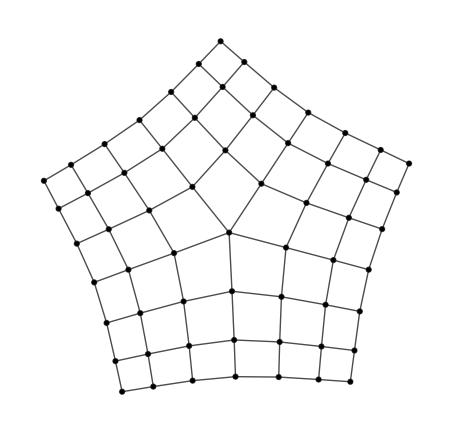

```mathematica
disc2={0<->{1,2},0<->{1,4},0<->{1,6},0<->{1,8},0<->{1,10}};
For[i=1,i≤4,i++,For[k=1,k≤10i-1,k++,AppendTo[disc2,{i,k}<->{i,k+1}]];AppendTo[disc2,{i,10i}<->{i,1}];For[j=1,j≤2i+1,j++,AppendTo[disc2,{i,j}<->{i+1,j+1}]];For[j=2i+1,j≤4i+1,j++,AppendTo[disc2,{i,j}<->{i+1,j+3}]];For[j=4i+1,j≤6i+1,j++,AppendTo[disc2,{i,j}<->{i+1,j+5}]];
For[j=6i+1,j≤8i+1,j++,AppendTo[disc2,{i,j}<->{i+1,j+7}]];
For[j=8i+1,j≤10i,j++,AppendTo[disc2,{i,j}<->{i+1,j+9}]];
AppendTo[disc2,{i,1}<->{i+1,10(i+1)}]]
L=3;
disc2=disc2[[1;;5L(L+1)+Sum[5(2i-1),{i,1,L}]]];
Graph[disc2,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

```mathematica
(*C_{4} +-90 [a]=1*)
```

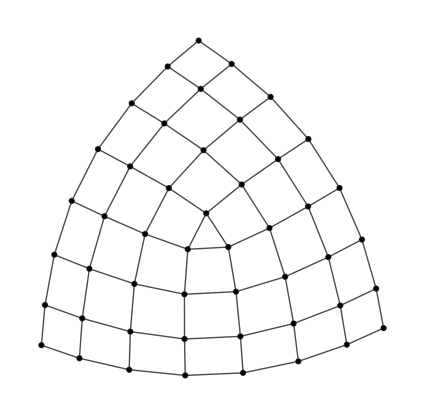

```mathematica
disc3={};
For[i=0,i≤3,i++,For[k=1,k<3(2i+1),k++,AppendTo[disc3,{i,k}<->{i,k+1}]];AppendTo[disc3,{i,1}<->{i,3(2i+1)}];For[j=1,j≤2i+2,j++,AppendTo[disc3,{i,j}<->{i+1,j+1}]];For[j=2i+2,j≤2(2i+1)+1,j++,AppendTo[disc3,{i,j}<->{i+1,j+3}]];For[j=2(2i+1)+1,j≤3(2i+1),j++,AppendTo[disc3,{i,j}<->{i+1,j+5}]];
AppendTo[disc3,{i,1}<->{i+1,3(2i+3)}]]
L=3;
disc3=disc3[[1;;Sum[3(2i+1)+6i,{i,0,L}]]];
Graph[disc3,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

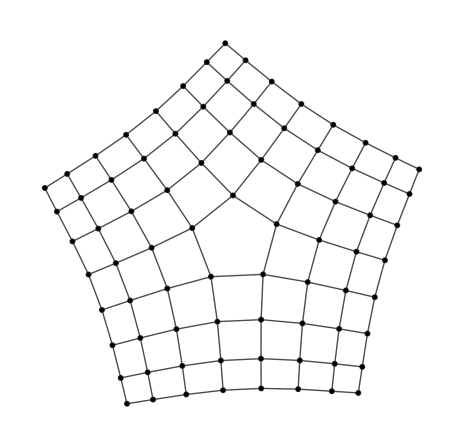

```mathematica
disc4={};
For[i=0,i≤3,i++,For[k=1,k<5(2i+1),k++,AppendTo[disc4,{i,k}<->{i,k+1}]];AppendTo[disc4,{i,1}<->{i,5(2i+1)}];For[j=1,j≤2i+2,j++,AppendTo[disc4,{i,j}<->{i+1,j+1}]];For[j=2i+2,j≤2(2i+1)+1,j++,AppendTo[disc4,{i,j}<->{i+1,j+3}]];For[j=2(2i+1)+1,j≤3(2i+1)+1,j++,AppendTo[disc4,{i,j}<->{i+1,j+5}]];
For[j=3(2i+1)+1,j≤4(2i+1)+1,j++,AppendTo[disc4,{i,j}<->{i+1,j+7}]];
For[j=4(2i+1)+1,j≤5(2i+1),j++,AppendTo[disc4,{i,j}<->{i+1,j+9}]];
AppendTo[disc4,{i,1}<->{i+1,5(2i+3)}]]
L=3;
disc4=disc4[[1;;Sum[5(2i+1)+10i,{i,0,L}]]];
Graph[disc4,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

```mathematica
(*C_{2} 180 [a]=(0,0)&(1,1)*)
```

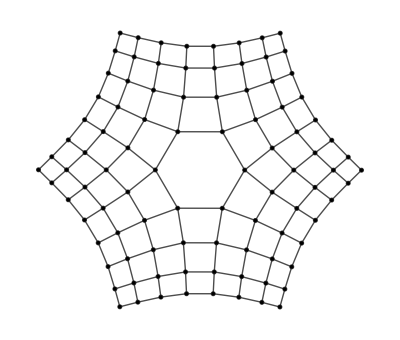

```mathematica
disc5={};
For[i=0,i≤3,i++,For[k=1,k<6(2i+1),k++,AppendTo[disc5,{i,k}<->{i,k+1}]];AppendTo[disc5,{i,1}<->{i,6(2i+1)}];For[j=1,j≤2i+2,j++,AppendTo[disc5,{i,j}<->{i+1,j+1}]];For[j=2i+2,j≤2(2i+1)+1,j++,AppendTo[disc5,{i,j}<->{i+1,j+3}]];For[j=2(2i+1)+1,j≤3(2i+1)+1,j++,AppendTo[disc5,{i,j}<->{i+1,j+5}]];
For[j=3(2i+1)+1,j≤4(2i+1)+1,j++,AppendTo[disc5,{i,j}<->{i+1,j+7}]];
For[j=4(2i+1)+1,j≤5(2i+1)+1,j++,AppendTo[disc5,{i,j}<->{i+1,j+9}]];
For[j=5(2i+1)+1,j≤6(2i+1),j++,AppendTo[disc5,{i,j}<->{i+1,j+11}]];
AppendTo[disc5,{i,1}<->{i+1,6(2i+3)}]]
L=3;
disc5=disc5[[1;;Sum[6(2i+1)+12i,{i,0,L}]]];
Graph[disc5,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

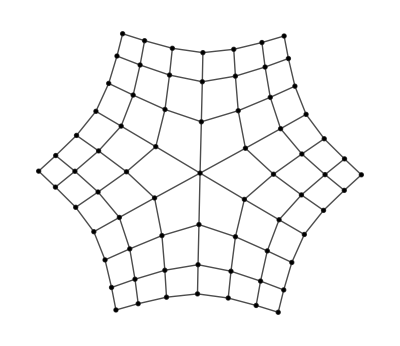

```mathematica
disc6={0<->{1,2},0<->{1,4},0<->{1,6},0<->{1,8},0<->{1,10},0<->{1,12}};
For[i=1,i≤4,i++,For[k=1,k≤12i-1,k++,AppendTo[disc6,{i,k}<->{i,k+1}]];AppendTo[disc6,{i,12i}<->{i,1}];For[j=1,j≤2i+1,j++,AppendTo[disc6,{i,j}<->{i+1,j+1}]];For[j=2i+1,j≤4i+1,j++,AppendTo[disc6,{i,j}<->{i+1,j+3}]];For[j=4i+1,j≤6i+1,j++,AppendTo[disc6,{i,j}<->{i+1,j+5}]];
For[j=6i+1,j≤8i+1,j++,AppendTo[disc6,{i,j}<->{i+1,j+7}]];
For[j=8i+1,j≤10i+1,j++,AppendTo[disc6,{i,j}<->{i+1,j+9}]];
For[j=10i+1,j≤12i,j++,AppendTo[disc6,{i,j}<->{i+1,j+11}]];
AppendTo[disc6,{i,1}<->{i+1,12(i+1)}]]
L=3;
disc6=disc6[[1;;6L(L+1)+Sum[6(2i-1),{i,1,L}]]];
Graph[disc6,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

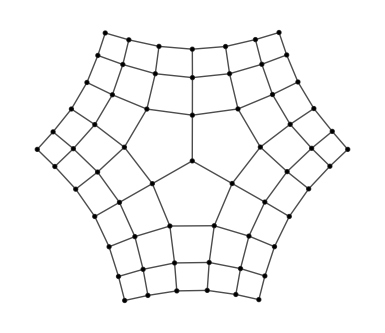

```mathematica
(*C_{2} 180 [a]=(0,1)&(1,0)*)
disc7={0<->{1,2},0<->{1,5},0<->{1,8}};
For[i=1,i≤4,i++,For[k=1,k<3(2i+1)+6(i-1),k++,AppendTo[disc7,{i,k}<->{i,k+1}]];
AppendTo[disc7,{i,1}<->{i,3(2i+1)+6(i-1)}];
For[j=1,j≤2i+1,j++,AppendTo[disc7,{i,j}<->{i+1,j+1}]];
For[j=2i+1,j≤2i+2(i-1)+2,j++,AppendTo[disc7,{i,j}<->{i+1,j+3}]];
For[j=2i+2(i-1)+2,j≤2(2i+1)+2(i-1),j++,AppendTo[disc7,{i,j}<->{i+1,j+5}]];
For[j=2(2i+1)+2(i-1),j≤2(2i+1)+4(i-1)+1,j++,AppendTo[disc7,{i,j}<->{i+1,j+7}]];For[j=2(2i+1)+4(i-1)+1,j≤3(2i+1)+4(i-1),j++,AppendTo[disc7,{i,j}<->{i+1,j+9}]];
For[j=3(2i+1)+4(i-1),j≤3(2i+1)+6(i-1),j++,AppendTo[disc7,{i,j}<->{i+1,j+11}]];
AppendTo[disc7,{i,1}<->{i+1,3(2i+3)+6i}]]
L=3;
disc7=disc7[[1;;Sum[24i-12,{i,1,L}]]];
Graph[disc7,EdgeStyle->{Thickness[0.001],Black},VertexStyle->Black]
```

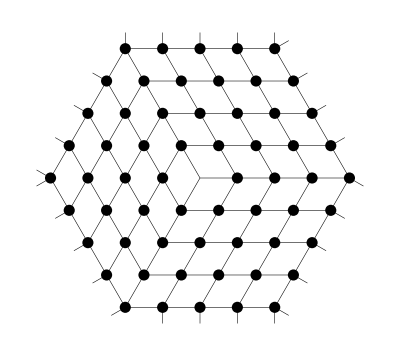

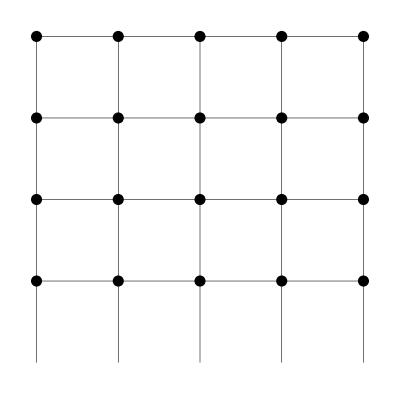

```mathematica
r1={1,0};
r2={0,1};
PTsize=0.02;
L=4;
NN=4;
Nomega=-1;
Nq=NN+Nomega;
Rot[r_,ϕ_]:={{Cos[ϕ],Sin[ϕ]},{-Sin[ϕ],Cos[ϕ]}}.r;
r0=Rot[r2,-π/6];
(*rotate coordinate*)

Mypatch[Length_,r0_,θ1_,θ2_,ϕ_]:={PointSize[PTsize],Table[Point[Rot[i*Rot[r1,θ1]+j*Rot[r2,θ2]+r0,ϕ]],{i,0,Length},{j,0,Length-1}]};
link[Length_,r0_,θ1_,θ2_,ϕ_]:={Thickness[0.001],Table[Line[{{Rot[i*Rot[r1,θ1]+j*Rot[r2,θ2]+r0,ϕ],Rot[(i+1)*Rot[r1,θ1]+j*Rot[r2,θ2]+r0,ϕ]}}],{i,0,Length-1},{j,0,Length-1}],Table[Line[{{Rot[i*Rot[r1,θ1]+j*Rot[r2,θ2]+r0,ϕ],Rot[(i)*Rot[r1,θ1]+(j+1)*Rot[r2,θ2]+r0,ϕ]}}],{i,0,Length},{j,-1,Length-2}]}
boundary[Length_,r0_,θ1_,θ2_,ϕ_]:={Thickness[0.001],Table[Line[{{Rot[Length*Rot[r1,θ1]+j*Rot[r2,θ2]+r0,ϕ],Rot[(Length+1/2)*Rot[r1,θ1]+(j+1/4)*Rot[r2,θ2]+r0,ϕ]}}],{j,0,Length-1}],Table[Line[{{Rot[i*Rot[r1,θ1]+(Length-1)*Rot[r2,θ2]+r0,ϕ],Rot[(i+1/4)*Rot[r1,θ1]+(Length-1/2)*Rot[r2,θ2]+r0,ϕ]}}],{i,0,Length}]}
Graphics[Table[{Mypatch[L,r0,0,-π/6,nq*2 π/Nq],link[L,r0,0,-π/6,nq*2 π/Nq],boundary[L,r0,0,-π/6,nq*2 π/Nq]},{nq,0,Nq-1}]]
Graphics[Table[{Mypatch[L,r0,0,0,nq*2 π/Nq],link[L,r0,0,0,nq*2 π/Nq]},{nq,0,0}]]
```

```mathematica
pts={};
For[i=0,i≤L,i++,For[j=i-L,j≤L-i,j++,AppendTo[pts,{Sqrt[2]i/2,Sqrt[2]j/2}]]];
For[i=-L,i≤0,i++,For[j=-i-L,j≤L+i,j++,AppendTo[pts,{Sqrt[2]i/2,Sqrt[2]j/2}]]];
link={};
For[i=0,i≤L-1,i++,For[j=0,j≤L-i-1,j++,AppendTo[link,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2]j/2}}];AppendTo[link,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i)/2,Sqrt[2](j+1)/2}}];
AppendTo[link,{{Sqrt[2](i+1)/2,Sqrt[2]j/2},{Sqrt[2](i)/2,Sqrt[2](j+1)/2}}]]];
For[i=0,i≤L-1,i++,For[j=i-L+1,j≤0,j++,AppendTo[link,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2]j/2}}];AppendTo[link,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i)/2,Sqrt[2](j-1)/2}}];AppendTo[link,{{Sqrt[2](i)/2,Sqrt[2](j-1)/2},{Sqrt[2](i+1)/2,Sqrt[2](j)/2}}]]];
For[i=-L,i≤-1,i++,For[j=0,j≤L+i,j++,AppendTo[link,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2]j/2}}];AppendTo[link,{{Sqrt[2](i+1)/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2](j+1)/2}}];AppendTo[link,{{Sqrt[2](i)/2,Sqrt[2](j)/2},{Sqrt[2](i+1)/2,Sqrt[2](j+1)/2}}]]];
For[i=-L,i≤-1,i++,For[j=-L-i,j≤0,j++,AppendTo[link,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2]j/2}}];
AppendTo[link,{{Sqrt[2](i)/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2](j-1)/2}}]]];
For[i=-L,i≤-1,i++,For[j=-L-i,j≤-1,j++,AppendTo[link,{{Sqrt[2](i)/2,Sqrt[2]j/2},{Sqrt[2](i)/2,Sqrt[2](j+1)/2}}]]];
```

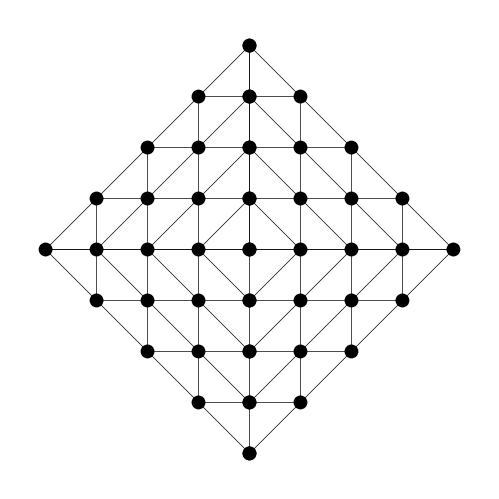

```mathematica
Graphics[{PointSize[PTsize],Point[pts],Thickness[0.001],Line[link]}]
```

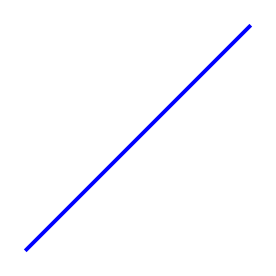

```mathematica
Graphics[{Thickness[0.01],Blue,Line[{{-2Sqrt[2],0},{0,2Sqrt[2]}}]}]
```

```mathematica
Point[Table[{Sqrt[2]i/2,Sqrt[2]j/2},{i,0,4},{j,0,i}]]
```

Point[{{{0,0}},{{1/(√2),0},{1/(√2),1/(√2)}},{{√2,0},{√2,1/(√2)},{√2,√2}},{{3/(√2),0},{3/(√2),1/(√2)},{3/(√2),√2},{3/(√2),3/(√2)}},{{2 √2,0},{2 √2,1/(√2)},{2 √2,√2},{2 √2,3/(√2)},{2 √2,2 √2}}}]

```mathematica
Table[{Sqrt[2]i/2,Sqrt[2]j/2},{i,0,4},{j,0,i}][[2]]
```

{{1/(√2),0},{1/(√2),1/(√2)}}

```mathematica
cc={};
```

```mathematica
For[i=-L,i≤-1,i++,For[j=0,j≤L+i,j++,AppendTo[cc,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i+1)/2,Sqrt[2]j/2}}];AppendTo[cc,{{Sqrt[2]i/2,Sqrt[2]j/2},{Sqrt[2](i)/2,Sqrt[2](j+1)/2}}];AppendTo[cc,{{Sqrt[2](i)/2,Sqrt[2](j)/2},{Sqrt[2](i+1)/2,Sqrt[2](j+1)/2}}]]];
```

```mathematica
cc
```

{{{-3/(√2),0},{-√2,0}},{{-3/(√2),0},{-3/(√2),1/(√2)}},{{-3/(√2),0},{-√2,1/(√2)}},{{-√2,0},{-1/(√2),0}},{{-√2,0},{-√2,1/(√2)}},{{-√2,0},{-1/(√2),1/(√2)}},{{-√2,1/(√2)},{-1/(√2),1/(√2)}},{{-√2,1/(√2)},{-√2,√2}},{{-√2,1/(√2)},{-1/(√2),√2}},{{-1/(√2),0},{0,0}},{{-1/(√2),0},{-1/(√2),1/(√2)}},{{-1/(√2),0},{0,1/(√2)}},{{-1/(√2),1/(√2)},{0,1/(√2)}},{{-1/(√2),1/(√2)},{-1/(√2),√2}},{{-1/(√2),1/(√2)},{0,√2}},{{-1/(√2),√2},{0,√2}},{{-1/(√2),√2},{-1/(√2),3/(√2)}},{{-1/(√2),√2},{0,3/(√2)}}}